```mathematica
SetsToSymbol2[s_]:=Symbol["v"<>StringRiffle[Map[Row[Map[ToString[IntegerString[#,20]]&,#]]&,s],"x"]]
```

```mathematica
IntegerString[13,16]
```

d

```mathematica
SymbolToSets[v1x2x3x4x5x6x7x8x9bxaxc]//SetsToSymbol2
```

v1x2x3x4x5x6x7x8x9bxaxc

```mathematica
SymbolToLabel3[s_,nodeCount_:5]:=Block[{blocks=StringSplit[StringDrop[SymbolName[s ],1],"x"]},
blocks=Select[blocks,StringLength[#]>1&];
If[Length[blocks]==0,
Style[OverHat[1],Darker[Darker[Red]],12]
,
If[StringLength[blocks[[1]]]==nodeCount,
Style[OverHat[0],Darker[Darker[Red]],12]
,
Row[Riffle[blocks ,Style["♁",Darker[Darker[Green]],12]]]
]
]
]
```

```mathematica
FormulaGraph2[formula_]:=Block[{sets=Map[SymbolToSets[#]&,ListofVars[formula]], edges={},vertices,vert={}},
Table[
Table[
If[IsRefinement[s1,s2]&&(Length[s1]==Length[s2]-1), AppendTo[edges,SetsToSymbol2[s2]->SetsToSymbol2[s1]]]
,{s2,Select[sets,#≠s1&]}
]
,{s1,sets}];
vert = Table[SetsToSymbol2[s],{s,sets}];
vertices = Table[SetsToSymbol2[s]-> SymbolToLabel3[ SetsToSymbol2[s]],{s,sets}];
Graph[vert,edges,VertexLabels->vertices,  ImageSize->{200,200}]
]
```

```mathematica
VertexList[Graph[plantri[[1]]]]
```

{1,2,3,4,5,6,7,8,9,10,11,12}

```mathematica
f001=FindFullFormula[VertexDelete[Graph[plantri[[1]]],12]]
```

{v1x2x3x4x5x6x7x8x9xaxb,v1x2x3x4x5x6x7x8x9bxa,v1x2x3x4x5x6x7x8bx9xa,v1x2x3x4x5x6x7x8ax9xb,v1x2x3x4x5x6x7x8ax9b,v1x2x3x4x5x6x7ax8x9xb,v1x2x3x4x5x6x7ax8x9b,v1x2x3x4x5x6x7ax8bx9,v1x2x3x4x5x6x79x8xaxb,v1x2x3x4x5x6x79x8bxa,v1x2x3x4x5x6x79x8axb,v1x2x3x4x5x6ax7x8x9xb,v1x2x3x4x5x6ax7x8x9b,v1x2x3x4x5x6ax7x8bx9,v1x2x3x4x5x6ax79x8xb,v1x2x3x4x5x6ax79x8b,v1x2x3x4x5x69x7x8xaxb,v1x2x3x4x5x69x7x8bxa,v1x2x3x4x5x69x7x8axb,7467,v35x69x8xa17xb24,v17x24x35x69x8bxa,v24x35x69x8bxa17,v17x24x35x69x8axb,v17x35x69x8axb24,v17x24x35x68x9xaxb,v17x35x68x9xaxb24,v17x24x35x9xa68xb,v17x35x9xa68xb24,v24x35x68x9xa17xb,v35x68x9xa17xb24,v24x35x68x917xaxb,v35x68x917xaxb24,v24x35x917xa68xb,v35x917xa68xb24,v17x24x35x68x9bxa,v17x24x35x9bxa68,v24x35x68x9bxa17}
 |  |  |  |

```mathematica
ChromaticPolynomial[VertexDelete[Graph[plantri[[1]]],12],3]
```

0

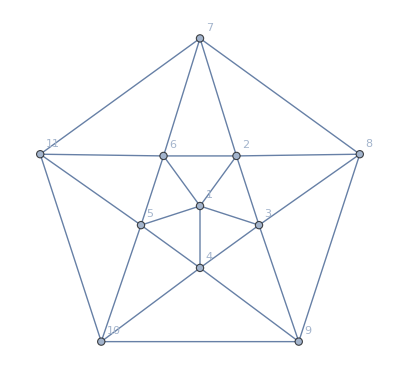

```mathematica
Graph[VertexDelete[Graph[plantri[[1]]],12],GraphLayout->"TutteEmbedding", VertexLabels->"Name"]
```

```mathematica
f001b=Select[f001,2<=StringCount[SymbolName[#],"x"]<4&]
```

{v1bx846x925xa37,v1ax735x846xb29,v2ax735x846xb19,v25x846xa37xb19,v19x735xa68xb24,v24x735xa68xb19,v46x735xa18xb29,v46x925xa37xb18,v47x925xa36xb18,v18x957xa36xb24,v24x957xa36xb18,v36x957xa18xb24,v69x735xa18xb24,v35x846xa17xb29,v3bx846x925xa17,v17x925xa36xb48,v36x925xa17xb48,v25x917xa36xb48,v58x917xa36xb24,v35x917xa68xb24}

```mathematica
TableForm[Map[SymbolToLabel2,f001b]//Sort]
```

17♁925♁a36♁b48
18♁957♁a36♁b24
19♁735♁a68♁b24
1a♁735♁846♁b29
1b♁846♁925♁a37
24♁735♁a68♁b19
24♁957♁a36♁b18
25♁846♁a37♁b19
25♁917♁a36♁b48
2a♁735♁846♁b19
35♁846♁a17♁b29
35♁917♁a68♁b24
36♁925♁a17♁b48
36♁957♁a18♁b24
3b♁846♁925♁a17
46♁735♁a18♁b29
46♁925♁a37♁b18
47♁925♁a36♁b18
58♁917♁a36♁b24
69♁735♁a18♁b24

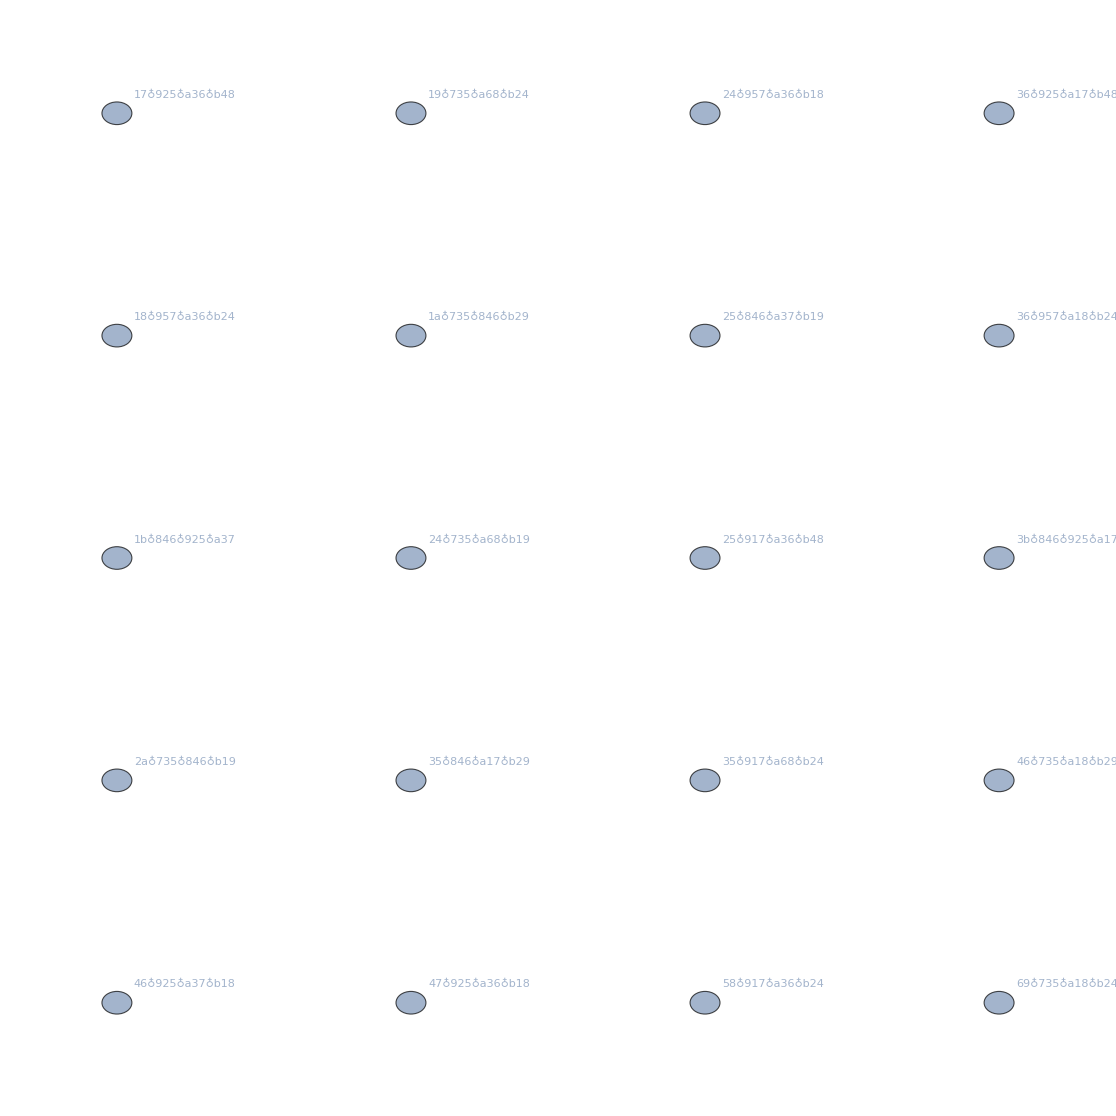

```mathematica
FormulaGraph2[f001b]
```